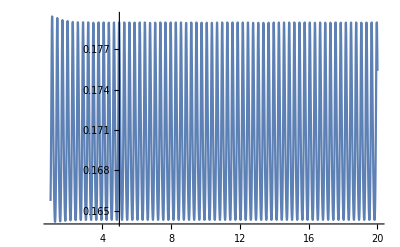
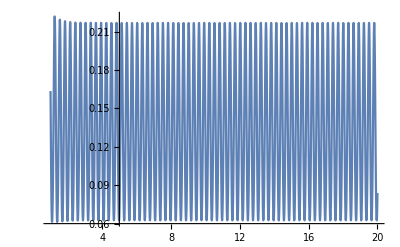
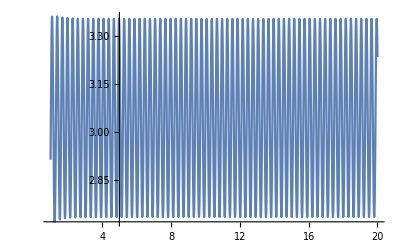
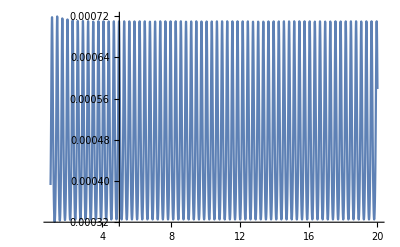
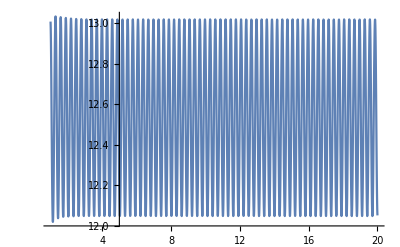
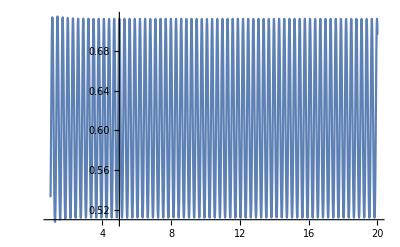
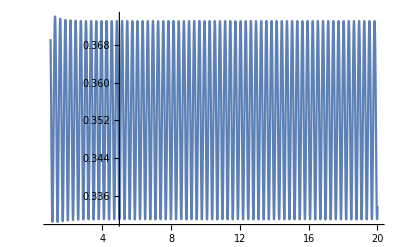
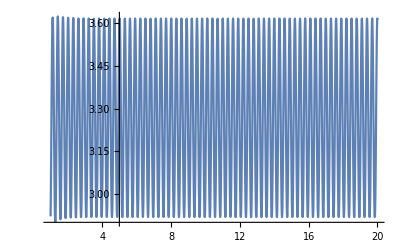

```mathematica
(*change the glucose concentration (Gluco) from 10 to 2, to reach the hopf bifurcation point*)
ClearAll["Global`*"]
variables = {
ACE[t], AMP[t], ATP[t], BPG[t], F16P[t], F6P[t], G3P[t], G6P[t], GLCi[t], NADH[t], P2G[t], P3G[t], PEP[t], PYR[t], TRIO[t]
};

initialValues = {
ACE[0] == 0.0320190578411, AMP[0] == 0.169126793522, ATP[0] == 2.88896546881, BPG[0] == 0.000272378466415, F16P[0] == 5.1230306063, F6P[0] == 1.35316959718, G3P[0] == 1.51464838664, G6P[0] == 5.2330035355, GLCi[0] == 0.0264527982732, NADH[0] == 0.570243405518, P2G[0] == 0.0219411145028, P3G[0] == 0.182294273857, PEP[0] == 0.0180777173497, PYR[0] == 2.26719823412, TRIO[0] == 2.6506857804
};

rates = { v GLT,v GLK,v GLYCO,v Treha,
v PGI, v PFK,v ALD,v G3PDH, v G3PA,
v GAPDH, v PGK, v PGM,  v ENO,v PYK,
v PDC, v SUC, v ADH,   v ATP,v AK};

rateEquations = {
v ADH -> -((VmADH*(ETOH*NAD - (ACE[t]*NADH[t])/KeqADH))/(KiADHNAD*KmADHETOH*(1 + (ETOH*KmADHNAD)/(KiADHNAD*KmADHETOH) + NAD/KiADHNAD + (ETOH*NAD)/(KiADHNAD*KmADHETOH) + (KmADHNADH*ACE[t])/(KiADHNADH*KmADHACE) + (ETOH*NAD*ACE[t])/(KiADHACE*KiADHNAD*KmADHETOH) + (KmADHNADH*NAD*ACE[t])/(KiADHNAD*KiADHNADH*KmADHACE) + NADH[t]/KiADHNADH + (ETOH*KmADHNAD*NADH[t])/(KiADHNAD*KiADHNADH*KmADHETOH) + (ACE[t]*NADH[t])/(KiADHNADH*KmADHACE) + (ETOH*ACE[t]*NADH[t])/(KiADHETOH*KiADHNADH*KmADHACE)))), v AK -> 133.333*(ADP^2 - (AMP[t]*ATP[t])/KeqAK), v ALD -> (VmALD*(F16P[t] - (KeqTPI*TRIO[t]^2)/(KeqALD*(1 + KeqTPI)^2)))/(KmALDF16P*(1 + F16P[t]/KmALDF16P + TRIO[t]/((1 + KeqTPI)*KmALDDHAP) + (KeqTPI*TRIO[t])/((1 + KeqTPI)*KmALDGAP) + (KeqTPI*F16P[t]*TRIO[t])/((1 + KeqTPI)*KmALDF16P*KmALDGAPi) + (KeqTPI*TRIO[t]^2)/((1 + KeqTPI)^2*KmALDDHAP*KmALDGAP))), v ATP -> (KATPASE*ATP[t]^nATP)/(KmATP^nATP + ATP[t]^nATP), v ENO -> (VmENO*(P2G[t] - PEP[t]/KeqENO))/(KmENOP2G*(1 + P2G[t]/KmENOP2G + PEP[t]/KmENOPEP)), v G3PA -> (VmG3PA*G3P[t])/(KmG3PAG3P*(1 + Phi/KmG3PAPhi)*(1 + G3P[t]/KmG3PAG3P)), v G3PDH -> (VmG3PDH*(-((NAD*G3P[t])/KeqG3PDH) + (NADH[t]*TRIO[t])/(1 + KeqTPI)))/(KmG3PDHDHAP*KmG3PDHNADH*(1 + ADP/KmG3PDHADP + ATP[t]/KmG3PDHATP + F16P[t]/KmG3PDHF16P)*(1 + NAD/KmG3PDHNAD + NADH[t]/KmG3PDHNADH)*(1 + G3P[t]/KmG3PDHG3P + TRIO[t]/((1 + KeqTPI)*KmG3PDHDHAP))), v GAPDH -> (-((VmGAPDHf*BPG[t]*NADH[t])/(KeqGAPDH*KmGAPDHGAP*KmGAPDHNAD)) + (KeqTPI*NAD*VmGAPDHf*TRIO[t])/((1 + KeqTPI)*KmGAPDHGAP*KmGAPDHNAD))/((1 + NAD/KmGAPDHNAD + NADH[t]/KmGAPDHNADH)*(1 + BPG[t]/KmGAPDHBPG + (KeqTPI*TRIO[t])/((1 + KeqTPI)*KmGAPDHGAP))), v GLK -> (VmGLK*(-((ADP*G6P[t])/KeqGLK) + ATP[t]*GLCi[t]))/(KmGLKATP*KmGLKGLCi*(1 + ADP/KmGLKADP + ATP[t]/KmGLKATP)*(1 + G6P[t]/KmGLKG6P + GLCi[t]/KmGLKGLCi)), v GLT -> (VmGLT*(GLCo - GLCi[t]/KeqGLT))/(KmGLTGLCo*(1 + GLCo/KmGLTGLCo + GLCi[t]/KmGLTGLCi + (alpha*GLCo*GLCi[t])/(KmGLTGLCi*KmGLTGLCo))), v GLYCO -> KGLYCOGEN*ATP[t]*G6P[t], v PDC -> (VmPDC*PYR[t]^nPDC)/(KmPDCPYR^nPDC*(1 + PYR[t]^nPDC/KmPDCPYR^nPDC)), v PFK -> (gR*VmPFK*ATP[t]*F6P[t]*(1 + ATP[t]/KmPFKATP + F6P[t]/KmPFKF6P + (gR*ATP[t]*F6P[t])/(KmPFKATP*KmPFKF6P)))/(KmPFKATP*KmPFKF6P*((L0*(1 + (CPFKAMP*AMP[t])/KPFKAMP)^2*(1 + (CiPFKATP*ATP[t])/KiPFKATP)^2*(1 + (CPFKATP*ATP[t])/KmPFKATP)^2*(1 + (CPFKF26BP*F26BP)/KPFKF26BP + (CPFKF16BP*F16P[t])/KPFKF16BP)^2)/((1 + AMP[t]/KPFKAMP)^2*(1 + ATP[t]/KiPFKATP)^2*(1 + F26BP/KPFKF26BP + F16P[t]/KPFKF16BP)^2) + (1 + ATP[t]/KmPFKATP + F6P[t]/KmPFKF6P + (gR*ATP[t]*F6P[t])/(KmPFKATP*KmPFKF6P))^2)), v PGI -> (VmPGI*(-(F6P[t]/KeqPGI) + G6P[t]))/(KmPGIG6P*(1 + F6P[t]/KmPGIF6P + G6P[t]/KmPGIG6P)), v PGK -> (VmPGK*(ADP*KeqPGK*BPG[t] - ATP[t]*P3G[t]))/(KmPGKATP*KmPGKP3G*(1 + ADP/KmPGKADP + ATP[t]/KmPGKATP)*(1 + BPG[t]/KmPGKBPG + P3G[t]/KmPGKP3G)), v PGM -> (VmPGM*(-(P2G[t]/KeqPGM) + P3G[t]))/(KmPGMP3G*(1 + P2G[t]/KmPGMP2G + P3G[t]/KmPGMP3G)), v PYK -> (VmPYK*(ADP*PEP[t] - (ATP[t]*PYR[t])/KeqPYK))/(KmPYKADP*KmPYKPEP*(1 + ADP/KmPYKADP + ATP[t]/KmPYKATP)*(1 + PEP[t]/KmPYKPEP + PYR[t]/KmPYKPYR)), v SUC -> KSUCC*ACE[t], v Treha -> KTREHALOSE*ATP[t]*G6P[t]
};

parameters = {
AXPsum -> 4.1, CPFKAMP -> 0.0845, CPFKATP -> 3.0, CPFKF16BP -> 0.397, CPFKF26BP -> 0.0174, CiPFKATP -> 100.0, ETOH -> 50.0, EXTERNAL -> 0.0, F26BP -> 0.02, GLCo -> 10, KATPASE -> 68.8096317495,  KPFKAMP -> 0.0995, KPFKF16BP -> 0.111, KPFKF26BP -> 0.000682, KSUCC -> 19.6023811746,  KeqADH -> 6.9*^-05, KeqAK -> 0.45, KeqALD -> 0.069, KeqENO -> 6.7, KeqG3PDH -> 4300.0, KeqGAPDH -> 0.0056263906277, KeqGLK -> 3800.0, KeqGLT -> 1.0, KeqPGI -> 0.314, KeqPGK -> 3200.0, KeqPGM -> 0.19, KeqPYK -> 6500.0, KeqTPI -> 0.045, KiADHACE -> 1.1, KiADHETOH -> 90.0, KiADHNAD -> 0.92, KiADHNADH -> 0.031, KiPFKATP -> 0.65, KmADHACE -> 1.11, KmADHETOH -> 17.0, KmADHNAD -> 0.17, KmADHNADH -> 0.11, KmALDDHAP -> 2.4, KmALDF16P -> 0.3, KmALDGAP -> 2.0, KmALDGAPi -> 10.0, KmATP -> 0.263159506089, KmENOP2G -> 0.04, KmENOPEP -> 0.5, KmG3PAG3P -> 4.21421727097, KmG3PAPhi -> 0.798017147071, KmG3PDHADP -> 1.60537927993, KmG3PDHATP -> 0.568725492711, KmG3PDHDHAP -> 0.4, KmG3PDHF16P -> 4.77110176421, KmG3PDHG3P -> 1.08899464691, KmG3PDHNAD -> 0.93, KmG3PDHNADH -> 0.023, KmGAPDHBPG -> 0.0098, KmGAPDHGAP -> 0.21, KmGAPDHNAD -> 0.09, KmGAPDHNADH -> 0.06, KmGLKADP -> 0.23, KmGLKATP -> 0.15, KmGLKG6P -> 30.0, KmGLKGLCi -> 0.08, KmGLTGLCi -> 1.1918, KmGLTGLCo -> 1.1918, KmPDCPYR -> 4.33, KmPFKATP -> 0.71, KmPFKF6P -> 0.1, KmPGIF6P -> 0.3, KmPGIG6P -> 1.4, KmPGKADP -> 0.2, KmPGKATP -> 0.3, KmPGKBPG -> 0.003, KmPGKP3G -> 0.53, KmPGMP2G -> 0.08, KmPGMP3G -> 1.2, KmPYKADP -> 0.53, KmPYKATP -> 1.5, KmPYKPEP -> 0.14, KmPYKPYR -> 21.0, L0 -> 0.66, NADSUM -> 1.0, Phi -> 1.20470265921, VmADH -> 834.684820559, VmALD -> 232.895576807, VmENO -> 462.025180445, VmG3PA -> 542.319235827, VmGAPDHf -> 419.560093466, VmGLK -> 329.958304618, VmGLT -> 136.494419254, VmPDC -> 223.978775021, VmPFK -> 183.616866462, VmPGI -> 467.754325004, VmPGK -> 1419.49486841, VmPGM -> 2762.32037661, VmPYK -> 1751.9596196, alpha -> 0.91, gR -> 5.12, nATP -> 1.0, nPDC -> 1.9, default compartment -> 1.0,
VmG3PDH -> 477.924460922,KGLYCOGEN -> 1.68983106019, KTREHALOSE -> 0.754128480342
};

assignments = {
NAD -> NADSUM - NADH[t], ADP -> AXPsum - AMP[t] - ATP[t]
};

(* Time evolution *)
odes = {
ACE'[t] == 1.0*v PDC -2.0*v SUC -1.0*v ADH, 
AMP'[t] == 1.0*v AK , ATP'[t] == 1.0*v PGK +1.0*v PYK +1.0*v AK -1.0*v PFK -1.0*v ATP -4.0*v SUC -1.0*v GLYCO -1.0*v GLK -1.0*v Treha, 
BPG'[t] == 1.0*v GAPDH -1.0*v PGK, 
F16P'[t] == 1.0*v PFK -1.0*v ALD, 
F6P'[t] == 1.0*v PGI -1.0*v PFK,
 G3P'[t] == 1.0*v G3PDH -1.0*v G3PA,
 G6P'[t] == 1.0*v GLK -1.0*v PGI -1.0*v GLYCO -2.0*v Treha,
 GLCi'[t] == 1.0*v GLT -1.0*v GLK, 
NADH'[t] == 1.0*v GAPDH +3.0*v SUC -1.0*v G3PDH -1.0*v ADH,
 P2G'[t] == 1.0*v PGM -1.0*v ENO,
P3G'[t] == 1.0*v PGK -1.0*v PGM,
PEP'[t] == 1.0*v ENO -1.0*v PYK, 
PYR'[t] == 1.0*v PYK -1.0*v PDC, 
TRIO'[t] == 2.0*v ALD -1.0*v G3PDH -1.0*v GAPDH
};
timeCourse = NDSolve[Join[odes, initialValues]//.rateEquations//.assignments//.parameters, variables, {t, 0, 20}];

(* Steady-state solution initialized with result of time evolution *)
(*findRootEquations = odes /.D[_[t],t]->0;
findRootVariables = Partition[Flatten[{#, #/.timeCourse/.t->100} &/@variables],2];
steadyStateVariables = FindRoot[findRootEquations//.rateEquations//.assignments//.parameters, findRootVariables, MaxIterations->100]
fluxes = #//.assignments//.parameters/.steadyStateVariables&/@rateEquations*)

(* Plot the time evolution of the variables *)
plotTable=Table[Plot[variables[[i]]/.parameters/.timeCourse,{t,1,20},PlotLegends->variables[[i]],PlotRange->Full],{i,Length[variables]}]

ace[t_]:=ACE[t]/.parameters/.timeCourse;
amp[t_]:=AMP[t]/.parameters/.timeCourse;
atp[t_]:=ATP[t]/.parameters/.timeCourse;
bpg[t_]:=BPG[t]/.parameters/.timeCourse;
f16p[t_]:=F16P[t]/.parameters/.timeCourse;
f6p[t_]:=F6P[t]/.parameters/.timeCourse;
g3p[t_]:=G3P[t]/.parameters/.timeCourse;
g6p[t_]:=G6P[t]/.parameters/.timeCourse;
glci[t_]:=GLCi[t]/.parameters/.timeCourse;
nadh[t_]:=NADH[t]/.parameters/.timeCourse;
p2g[t_]:=P2G[t]/.parameters/.timeCourse;
p3g[t_]:=P3G[t]/.parameters/.timeCourse;
pep[t_]:=PEP[t]/.parameters/.timeCourse;
pyr[t_]:=PYR[t]/.parameters/.timeCourse;
trio[t_]:=TRIO[t]/.parameters/.timeCourse;
adp[t_]:=AXPsum-amp[t]-atp[t]/.parameters;
nad[t_]:=NADSUM-nadh[t]/.parameters;


Time0=Array[0.01 #1 +10&,400];
ace1=Mean[Table[ace[t],{t,Time0}]];
amp1=Mean[Table[amp[t],{t,Time0}]];
atp1=Mean[Table[atp[t],{t,Time0}]];
bpg1=Mean[Table[bpg[t],{t,Time0}]];
f16p1=Mean[Table[f16p[t],{t,Time0}]];
f6p1=Mean[Table[f6p[t],{t,Time0}]];
g3p1=Mean[Table[g3p[t],{t,Time0}]];
g6p1=Mean[Table[g6p[t],{t,Time0}]];
glci1=Mean[Table[glci[t],{t,Time0}]];
nadh1=Mean[Table[nadh[t],{t,Time0}]];
p2g1=Mean[Table[p2g[t],{t,Time0}]];
p3g1=Mean[Table[p3g[t],{t,Time0}]];
pep1=Mean[Table[pep[t],{t,Time0}]];
pyr1=Mean[Table[pyr[t],{t,Time0}]];
trio1=Mean[Table[trio[t],{t,Time0}]];
adp1=Mean[Table[adp[t],{t,Time0}]];
nad1=Mean[Table[nad[t],{t,Time0}]];



Plot[{(ace[t]-ace1)/ace1,(pyr[t]-pyr1)/pyr1,(nadh[t]-nadh1)/nadh1,(atp[t]-atp1)/atp1},{t,10,11},PlotRange->Full,PlotLegends->{"ACE","PYR","NADH","ATP"}]
```

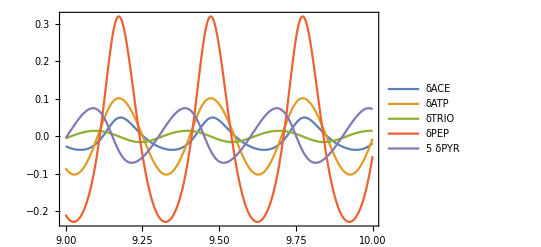

```mathematica
Plot[{(ace[t]-ace1)/ace1,(atp[t]-atp1)/atp1,(trio[t]-trio1)/trio1,(pep[t]-pep1)/pep1,5(pyr[t]-pyr1)/pyr1},{t,9,10},PlotRange->Full,PlotLegends->{"δACE","δATP","δTRIO","δPEP","5 δPYR"},BaseStyle->{FontSize->15},Frame->True]
```

(PDC | 149.565
PGK | 149.549
GAPDH | 149.549
PGM | 149.544
ENO | 149.543
PYK | 149.539
ADH | 142.882
GLK | 114.987
GLT | 114.985
ALD | 83.1133
PGI | 82.9958
PFK | 82.9641
ATPase | 63.3081
GLYCO | 16.8414
G3PP | 16.6971
G3PDH | 16.6902
Treha | 7.51588
GLYO | 3.34074
AK | -0.0242012)

(F16P | 12.5383
PYR | 6.25307
TRIO | 3.59333
G6P | 3.26165
ATP | 3.04295
F6P | 0.608274
 G3P | 0.352934
P3G | 0.294949
ACE | 0.170425
AMP | 0.13404
GLCi | 0.0691218
PEP | 0.062208
P2G | 0.0352333
NADH | 0.0294231
BPG | 0.000482214)

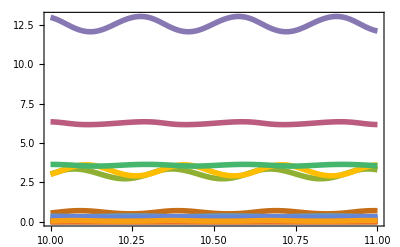

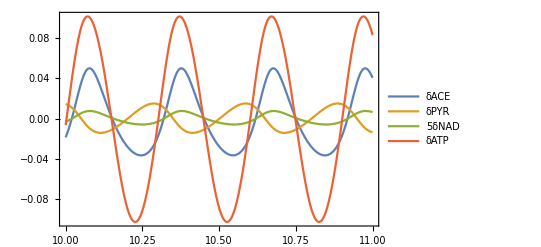

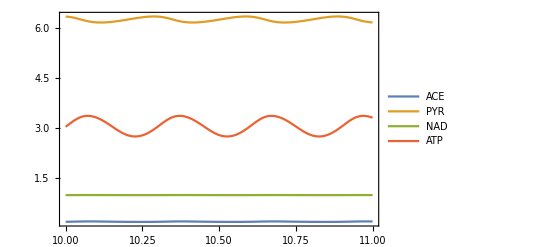

```mathematica
results=Mean[Table[rates//.rateEquations//.assignments//.parameters//.timeCourse,{t,Array[0.05 #1+9&,100]}]];
results2=Flatten[Flatten[results]];
MatrixForm[Reverse[SortBy[Transpose[{{"GLT","GLK","GLYCO","Treha",
"PGI", "PFK","ALD","G3PDH", "G3PP",
"GAPDH", "PGK", "PGM",  "ENO","PYK",
"PDC", "GLYO", "ADH",   "ATPase","AK"},results2}],Last]]]


results=Mean[Table[variables//.assignments//.parameters//.timeCourse,{t,Array[0.05 #1+9&,100]}]];
results2=Flatten[Flatten[results]];
MatrixForm[Reverse[SortBy[Transpose[{{"ACE","AMP", "ATP", "BPG", "F16P", "F6P"," G3P", "G6P", "GLCi","NADH", "P2G", "P3G", "PEP", "PYR", "TRIO"},results2}],Last]]]
Plot[{ace[t],amp[t],atp[t],bpg[t],f16p[t],f6p[t],g3p[t],g6p[t],glci[t],nadh[t],p2g[t],p3g[t],pep[t],pyr[t],trio[t] },{t,10,11},PlotRange->Full,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->15},Frame->True]

Plot[{(ace[t]-ace1)/ace1,  (pyr[t]-pyr1)/pyr1,5(nad[t]-nad1)/nad1,(atp[t]-atp1)/atp1},{t,10,11},PlotRange->Full,PlotLegends->{"δACE","δPYR","5δNAD","δATP"},BaseStyle->{FontSize->15},Frame->True]

Plot[{ace[t],  pyr[t],nad[t],atp[t]},{t,10,11},PlotRange->Full,PlotLegends->{"ACE","PYR","NAD","ATP"},BaseStyle->{FontSize->15},Frame->True]
```

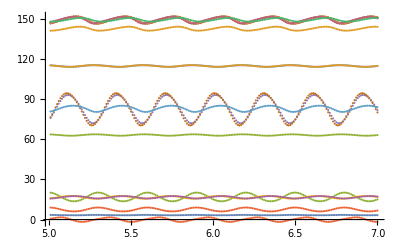

```mathematica
xx=Table[0.01 x+5,{x,200}];
result=Array[0 #1 &,19];
For[j=1,j<20,j++,result[[j]]=Flatten[Table[rates[[j]]//.rateEquations//.assignments//.parameters//.timeCourse,{t,xx}]]];
ListPlot[Table[Thread[{xx,result[[j]]}],{j,19}]]
```

```mathematica
result
```

```mathematica
results=Table[rates//.rateEquations//.assignments//.parameters//.timeCourse,{t,{10}}];
results2=Flatten[Flatten[results]];
MatrixForm[Reverse[SortBy[Transpose[{{"GLT","GLK","GLYCO","Treha",
"PGI", "PFK","ALD","G3PDH", "G3PP",
"GAPDH", "PGK", "PGM",  "ENO","PYK",
"PDC", "SUC", "ADH",   "ATPase","AK"},results2}],Last]]]
```

(GAPDH | 151.124
PGK | 151.12
PDC | 150.9
PGM | 150.712
ENO | 150.642
PYK | 150.322
ADH | 144.212
GLK | 115.157
GLT | 115.016
ALD | 83.8938
PGI | 80.8438
PFK | 78.9545
ATPase | 63.3053
G3PP | 17.1399
G3PDH | 16.7765
GLYCO | 15.4364
Treha | 6.88888
SUC | 3.28042
AK | -1.73489)